```mathematica
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->TraditionalForm}]
```

```mathematica
Get[NotebookDirectory[]<>"qct.m"]
```

QuarkContractionTool (QCT)

## Very simple Examples

```mathematica
Field[f,a,mu,x]**FieldB[f,b,nu,y]
```

f_mu^a(x)**(f̄)_nu^b(y)

```mathematica
QuarkContract[WickContract[%]]
```

S_munu^(f,ab)(y,x)

```mathematica
ToTeXForm[%]
```

S_{\mu \nu }^{f,ab}(y,x)

```mathematica
ToQDP[%%]
```

/* 
Result is of type SpinColorMatrix
{S^f(y,x) -> quarkProp1}
*/ 
quarkProp1

```mathematica
QuarkContract[WickContract[Pol[SI[{nu,mu}]]**Field[f,a,mu,x]**FieldB[f,b,nu,y]]]
```

(traceSpin(Pol.S^f(y,x)))^ab

```mathematica
QuarkContract[Eps[a,b,c] Eps[a',b',c'] Op[CI[{a,a'}],SI[{mu,nu}]]*Op'[CI[{b,b'}],SI[{mu,rho}]]]
```

quarkContract13_nurho^(c' c)(Op,Op')

## Λ-Baryon

```mathematica
OP=Eps[a,b,c]**(Gamma^A)[SI[{mu,alpha}]]**(2**Field[s,a,alpha,x]**Field[u,b,beta,x]**(Gamma^B)[SI[{beta,gamma}]]**Field[d,c,gamma,x]+Field[d,a,alpha,x]**Field[u,b,beta,x]**(Gamma^B)[SI[{beta,gamma}]]**Field[s,c,gamma,x]-Field[u,a,alpha,x]**Field[d,b,beta,x]**(Gamma^B)[SI[{beta,gamma}]]**Field[s,c,gamma,x])
```

ϵ^abc**(Gamma^A)_mualpha**(d_alpha^a(x)**u_beta^b(x)**(Gamma^B)_betagamma**s_gamma^c(x)-u_alpha^a(x)**d_beta^b(x)**(Gamma^B)_betagamma**s_gamma^c(x)+2**s_alpha^a(x)**u_beta^b(x)**(Gamma^B)_betagamma**d_gamma^c(x))

```mathematica
OPBar=Eps[a',b',c']**(2**FieldB[u,a',gamma',y]**(Gamma^BT)[SI[{beta',gamma'}]]**FieldB[d,b',beta',y]**FieldB[s,c',alpha',y]+FieldB[u,a',gamma',y]**(Gamma^BT)[SI[{beta',gamma'}]]**FieldB[s,b',beta',y]**FieldB[d,c',alpha',y]-FieldB[d,a',gamma',y]**(Gamma^BT)[SI[{beta',gamma'}]]**FieldB[s,b',beta',y]**FieldB[u,c',alpha',y])**(Gamma^A)[SI[{alpha',mu'}]]
```

ϵ^(a' b' c')**(-(d̄)_gamma'^a'(y)**(Gamma^BT)_beta'gamma'**(s̄)_beta'^b'(y)**(ū)_alpha'^c'(y)+(ū)_gamma'^a'(y)**(Gamma^BT)_beta'gamma'**(s̄)_beta'^b'(y)**(d̄)_alpha'^c'(y)+2**(ū)_gamma'^a'(y)**(Gamma^BT)_beta'gamma'**(d̄)_beta'^b'(y)**(s̄)_alpha'^c'(y))**(Gamma^A)_alpha'mu'

```mathematica
Timing[Contracted=WickContract[P[SI[{mu',mu}]]**OP**OPBar];]
```

{0.010977,Null}

```mathematica
Result=QuarkContract[Contracted];
ToQDP[Simplify[Result],{Gamma^B->GammaB,Gamma^A->GammaA,Gamma^BT->GammaBT}]
```

/* 
Result is of type Scalar
{S^d(y,x) -> quarkProp1, S^s(y,x) -> quarkProp2, S^u(y,x) -> quarkProp3}
*/ 
trace(quarkContract13(quarkProp1,GammaB*quarkProp2*GammaBT)*transposeSpin(GammaA*P*GammaA*quarkProp3)) + 2*trace(quarkContract13(quarkProp3,GammaB*quarkProp1)*transposeSpin(GammaA*P*GammaA*quarkProp2*GammaBT)) + trace(quarkContract13(quarkProp3,GammaB*quarkProp2*GammaBT)*transposeSpin(GammaA*P*GammaA*quarkProp1)) + 2*trace(quarkContract13(GammaB*quarkProp2,quarkProp1*GammaBT)*transposeSpin(GammaA*P*GammaA*quarkProp3)) - 2*trace(quarkContract13(quarkProp3,GammaB*quarkProp1)*GammaA*P*GammaA*quarkProp2*GammaBT) - 2*trace(quarkContract13(quarkProp3,GammaB*quarkProp2)*GammaA*P*GammaA*quarkProp1*GammaBT) - traceColor(traceSpin(quarkContract13(quarkProp1,GammaB*quarkProp2*GammaBT))*traceSpin(GammaA*P*GammaA*quarkProp3)) - 4*traceColor(traceSpin(quarkContract13(quarkProp3,GammaB*quarkProp1*GammaBT))*traceSpin(GammaA*P*GammaA*quarkProp2)) - traceColor(traceSpin(quarkContract13(quarkProp3,GammaB*quarkProp2*GammaBT))*traceSpin(GammaA*P*GammaA*quarkProp1))

Generating graphs

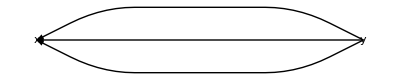

```mathematica
GraphWC[Contracted]
```

## Baryon 3 pt

```mathematica
J=.
```

```mathematica
OP=Eps[a,b,c]**OA[SI[{mu,alpha}]]**Field[u,a,alpha,y]**Field[u,b,beta,y]**GammaB[SI[{beta,gamma}]]**Field[d,c,gamma,y]
```

ϵ^abc**OA_mualpha**u_alpha^a(y)**u_beta^b(y)**GammaB_betagamma**d_gamma^c(y)

```mathematica
OPBar=-Eps[a',b',c']**FieldB[d,a',alpha',x]**GammaBT[SI[{alpha',beta'}]]**FieldB[u,b',beta',x]**FieldB[u,c',nu',x]**OAT[SI[{nu',mu'}]]
```

-ϵ^(a' b' c')**(d̄)_alpha'^a'(x)**GammaBT_alpha'beta'**(ū)_beta'^b'(x)**(ū)_nu'^c'(x)**OAT_nu'mu'

```mathematica
Jc=FieldB[d,f,sigma,z]**J[sigma,rho]**Field[d,f,rho,z]
```

(d̄)_sigma^f(z)**J(sigma,rho)**d_rho^f(z)

```mathematica
MatrixElement=OP**Jc**OPBar**P[mu',mu]
```

ϵ^abc**OA_mualpha**u_alpha^a(y)**u_beta^b(y)**GammaB_betagamma**d_gamma^c(y)**(d̄)_sigma^f(z)**J(sigma,rho)**d_rho^f(z)**(-ϵ^(a' b' c')**(d̄)_alpha'^a'(x)**GammaBT_alpha'beta'**(ū)_beta'^b'(x)**(ū)_nu'^c'(x)**OAT_nu'mu')**P(mu',mu)

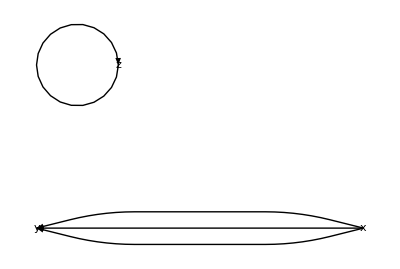
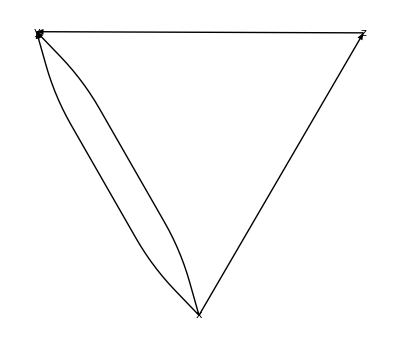

```mathematica
GraphWC[WickContract[MatrixElement]]
```

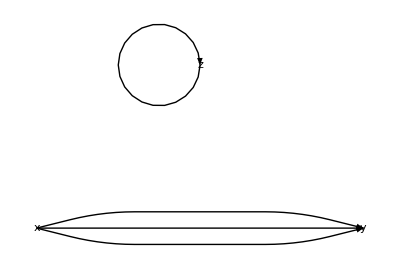
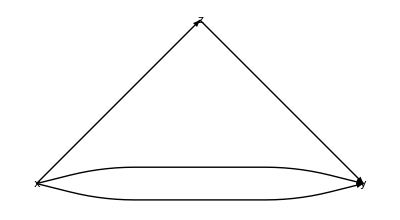

```mathematica
test=GraphWC[WickContract[MatrixElement],VertexCoordinateRules->{x->{-1,0},y->{1,0},z->{0,1}}]
```

### Remove disconnected pieces

```mathematica
MatrixElementContracted=WickContract[MatrixElement]/.DE[__,{a_,a_}][__]->0
```

OA_mualpha GammaBT_alpha'beta' GammaB_betagamma OAT_nu'mu' J(sigma,rho) P(mu',mu) (-ϵ^abc) ϵ^(a' b' c') (S_(beta beta')^(u,b b')(x,y) S_gammasigma^(d,cf)(z,y) S_(alpha nu')^(u,a c')(x,y) S_(rho alpha')^(d,f a')(x,z)-S_gammasigma^(d,cf)(z,y) S_(alpha beta')^(u,a b')(x,y) S_(rho alpha')^(d,f a')(x,z) S_(beta nu')^(u,b c')(x,y))

```mathematica
MatrixElementConnectedProj=Expand[MatrixElementContracted]/.J[sigma,rho]->DD[rho,sigma]
```

δ_rhosigma OA_mualpha GammaBT_alpha'beta' GammaB_betagamma OAT_nu'mu' P(mu',mu) ϵ^abc ϵ^(a' b' c') S_gammasigma^(d,cf)(z,y) S_(alpha beta')^(u,a b')(x,y) S_(rho alpha')^(d,f a')(x,z) S_(beta nu')^(u,b c')(x,y)-δ_rhosigma OA_mualpha GammaBT_alpha'beta' GammaB_betagamma OAT_nu'mu' P(mu',mu) ϵ^abc ϵ^(a' b' c') S_(beta beta')^(u,b b')(x,y) S_gammasigma^(d,cf)(z,y) S_(alpha nu')^(u,a c')(x,y) S_(rho alpha')^(d,f a')(x,z)

```mathematica
SeqProp=Contract[Expand[Uncontract[MatrixElementConnectedProj] DEProject[{d,d},{x,z}][CI[{a1,a2}],SI[{mu1,mu2}]]]]
```

ϵ^abc ϵ^(a1 b' c') S_(beta nu')^(u,b c')(x,y) (GammaB.S^d(z,y))_betamu2^ca2 (OAT.P.OA.S^u(x,y).Transpose[GammaBT])_nu'mu1^ab'-ϵ^abc ϵ^(a1 b' c') (GammaB.S^d(z,y))_betamu2^ca2 (OAT.P.OA.S^u(x,y))_nu'nu'^ac' (S^u(x,y).Transpose[GammaBT])_betamu1^bb'

### Rewrite the expression as MatrixElementConnected=(S^(u,b'a'))_β'μ(x,z)*(SeqProp^a'b')_μβ'(z,x)

```mathematica
QuarkContract[Uncontract[Contract[SeqProp]]*DEInverse[{d,d},{y,z}][CI[{a2,a3}],SI[{mu2,mu3}]]]//InputForm
```

(quarkContract[{1, 4}, OAT . P . OA . DE[{u, u}, {x, y}] . Transpose[GammaBT], 
    DE[{u, u}, {x, y}]] . GammaB)[CI[{a1, a3}], SI[{mu1, mu3}]] - 
 Eps[a, b, c]*Eps[a1, Derivative[1][b], Derivative[1][c]]*
  GammaB[CI[{c, a3}], SI[{beta, mu3}]]*(DE[{u, u}, {x, y}] . Transpose[GammaBT])[
   CI[{b, Derivative[1][b]}], SI[{beta, mu1}]]*traceSpin[OAT . P . OA . DE[{u, u}, {x, y}]][
   CI[{a, Derivative[1][c]}]]

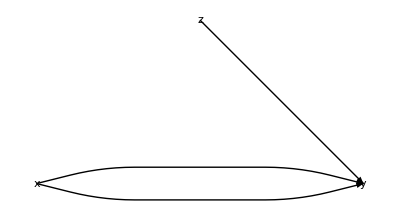

```mathematica
GraphWC[Uncontract[SeqProp],VertexCoordinateRules->{x->{-1,0},y->{1,0},z->{0,1}}]
```

### Three vector currents

```mathematica
cur[x_]:=FieldB[u,a,alpha,x]**Field[u,a,alpha,x]
```

```mathematica
cur3=WickContract[cur[Subscript[x, 1]]**cur[Subscript[x, 2]]**cur[Subscript[x, 3]]];
```

```mathematica
cur3
```

S_alphaalpha^(u,aa)(x_1,x_3) S_alphaalpha^(u,aa)(x_2,x_2) S_alphaalpha^(u,aa)(x_3,x_1)-S_alphaalpha^(u,aa)(x_1,x_2) S_alphaalpha^(u,aa)(x_2,x_3) S_alphaalpha^(u,aa)(x_3,x_1)-S_alphaalpha^(u,aa)(x_1,x_3) S_alphaalpha^(u,aa)(x_2,x_1) S_alphaalpha^(u,aa)(x_3,x_2)+S_alphaalpha^(u,aa)(x_1,x_1) S_alphaalpha^(u,aa)(x_2,x_3) S_alphaalpha^(u,aa)(x_3,x_2)+S_alphaalpha^(u,aa)(x_1,x_2) S_alphaalpha^(u,aa)(x_2,x_1) S_alphaalpha^(u,aa)(x_3,x_3)-S_alphaalpha^(u,aa)(x_1,x_1) S_alphaalpha^(u,aa)(x_2,x_2) S_alphaalpha^(u,aa)(x_3,x_3)

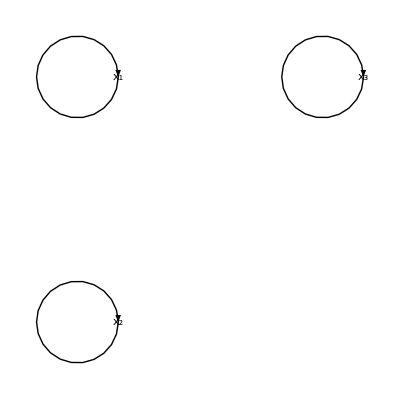
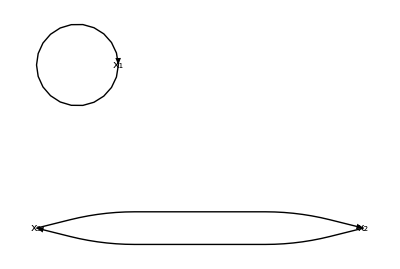
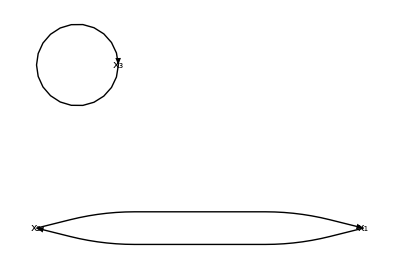
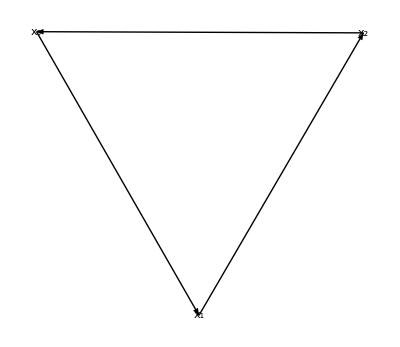
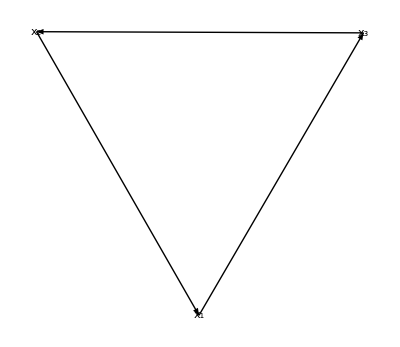
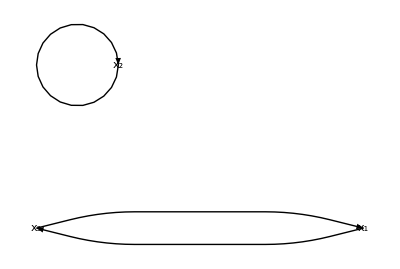

```mathematica
GraphWC[cur3]
```